# 私の血糖値の推移

### 経緯

1月末に、かかりつけ医にて重度の糖尿病症状が確認され直ちに入院となった。
状態は重度の糖尿病性ケトアシドーシス（極度の脱水、栄養失調、ケトーシス、高血糖）。昏睡していてもおかしくない状態だったらしい。
2週間の入院。治療は脱水状態の離脱からはじめられ、数日後より栄養状態の回復治療、ついで糖尿病治療を行なった。同時に合併症検査が行われた。
結果的に合併症はなし、退院後はインスリンによる治療と定期的な通院検査を行うものとなった。

退院後の治療は食前のインスリン投与、1日1回の高濃度インスリン投与、カロリーコントロール、血糖コントロール、を行う。

血糖は血糖測定器があり随時測定可能。食事前に血糖測定を行なっている。

本日は血糖値の測定についてと血糖値の推移について報告する。
- 周期性の確認
- ローパスによる血糖値の長期変動

### 血糖値の測定

```mathematica
jpg="/Users/kouamano/Profile/IMG_0085.jpg"
```

/Users/kouamano/Profile/IMG_0085.jpg

下の写真が血糖値の測定器（左が測定器とチップ、右が穿刺具と穿刺針）。

血糖値の測定は、まず穿刺具にて指先に穿刺し、血液を測定器のチップに塗布する。数秒で結果が出る。

測定器には過去数十件の値と測定時間が記録されており、NFCによりスマホに転送可能。転送されたスマホ側でエクセルデータを作成しさらにメール転送が可能。

```mathematica
Import[jpg]
```

-Graphics-

### Data

スマホから転送されてきたデータのファイル。

```mathematica
dir="/Users/kouamano/Profile/"
```

/Users/kouamano/Profile/

```mathematica
xlsfile="01_28_2022-04_27_2022.xls"
```

01_28_2022-04_27_2022.xls

### Import

ファイルから値を読み取る。

```mathematica
importData=Import[dir<>xlsfile];
```

```mathematica
selectedData[1]=Transpose[Transpose[Drop[importData[[1]],1]][[{1,3}]]];
```

```mathematica
ts=TimeSeries[selectedData[1]]
```

TimeSeries[…]

単純なプロット。

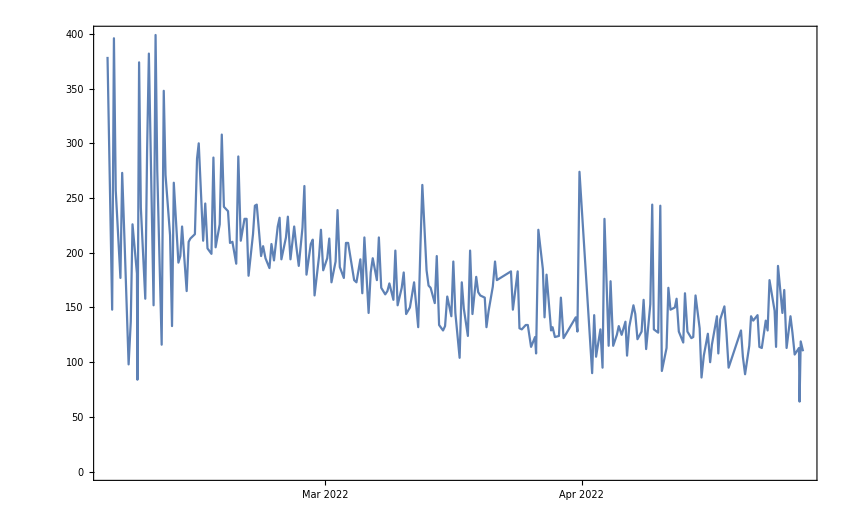

```mathematica
dlp=DateListPlot[ts]
```

### Interpolation

測定間隔がまばらなので間の値も推測できるよう補間関数を作成。実際の測定回数から平均の測定間隔を算出し用いる。

```mathematica
nts=Normal[ts];
```

```mathematica
nPts=Length[nts]
```

241

```mathematica
startDate=nts[[1,1]]
```

Wed 2 Feb 2022 16:45:00GMT+9

```mathematica
startTime=AbsoluteTime[nts[[1,1]]]
```

3852809100

```mathematica
endDate=nts[[-1,1]]
```

Wed 27 Apr 2022 18:42:00GMT+9

```mathematica
endTime=AbsoluteTime[nts[[-1,1]]]
```

3860073720

```mathematica
period=(endTime-startTime)/nPts//N
```

30143.7

```mathematica
endDate-startDate
```

84.0813 days

```mathematica
nPts/(endDate-startDate)
```

2.86628 per day

### Fourier

period 1

適当な間隔にて等間隔で補間してplot、うまくいっているか確認。

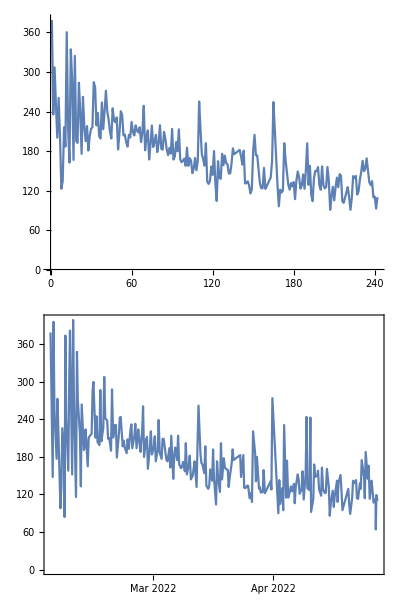

```mathematica
Grid[{{ListLinePlot[Table[Interpolation[ts][t],{t,startTime,endTime,period}]]},{dlp}}]
```

低周波側に大きなピークが見られる。このような場合、強い周期性がないことを示唆している。

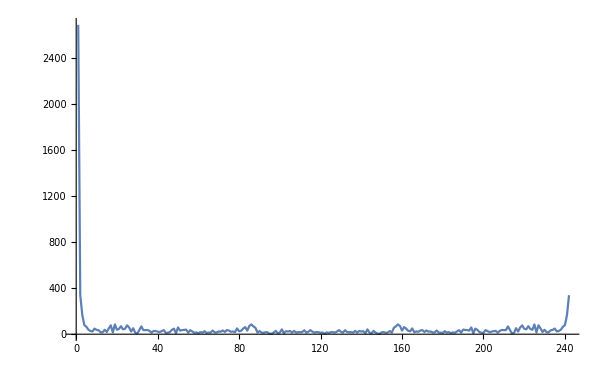

```mathematica
ListLinePlot[(fou=Fourier[Table[Interpolation[ts][t],{t,startTime,endTime,period}]])//Abs,PlotRange->Full]
```

低周波側を除き、ある程度の強度がある周波数を確認する。20回弱の部分にピークが見られる。

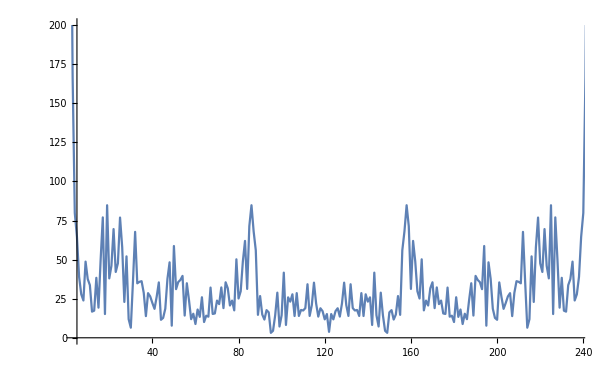

```mathematica
ListLinePlot[Fourier[Table[Interpolation[ts][t],{t,startTime,endTime,period}]]//Abs,PlotRange->{{5,nPts-5},{0,200}}]
```

```mathematica
af=Abs[Fourier[Table[Interpolation[ts][t],{t,startTime,endTime,period}]]];
```

```mathematica
max=Max[af[[5;;nPts-5]]]
```

84.7781

```mathematica
Position[af,max]
```

{{86},{158}}

85回の繰り返し、1日の周期。

```mathematica
(endTime-startTime)/60/60/24/(86-1)//N
```

0.989191

もう一つ、20回前後の部分にピークが見られる。

```mathematica
TakeLargest[af[[5;;nPts-5]],9]
```

{84.7781,84.7781,84.7695,84.7695,77.0011,77.0011,76.9034,76.9034,71.3752}

```mathematica
max2=TakeLargest[af[[5;;nPts-5]],4][[-1]]
```

84.7695

```mathematica
Position[af,max2]
```

{{19},{225}}

18回の繰り返し、4.7日周期。

```mathematica
(endTime-startTime)/60/60/24/(19-1)//N
```

4.67118

period 2

1日4回の測定データを擬似的に作成。（おおよそ6、12、18時に測定しているので、24時の測定値を仮想的に作る）

```mathematica
period2=(endTime-startTime)/(endDate-startDate)[[1]]/4 (*1日4回*)
```

21600.

```mathematica
nPts2=(endTime-startTime)/period2
```

336.325

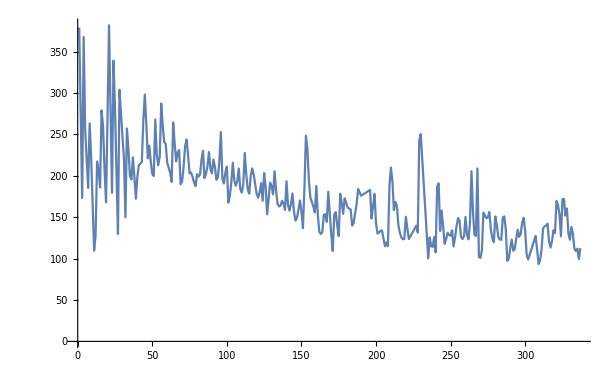

```mathematica
ListLinePlot[Table[Interpolation[ts][t],{t,startTime,endTime,period2}]]
```

あまり変わらない。20回前後の周波数の方が強くなった。

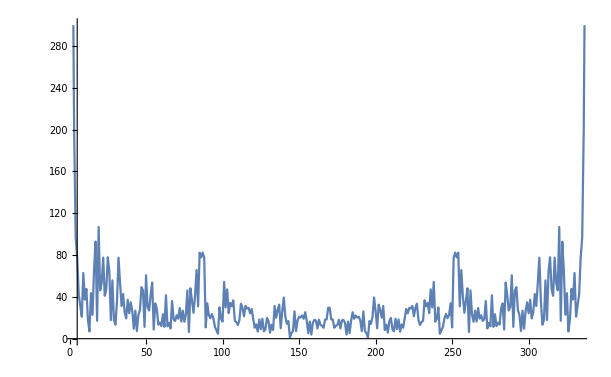

```mathematica
ListLinePlot[Fourier[Table[Interpolation[ts][t],{t,startTime,endTime,period2}]]//Abs,PlotRange->{{5,nPts2-5},{0,300}}]
```

### ローパス

period 1

まず、逆フーリエで再現できるか確認。

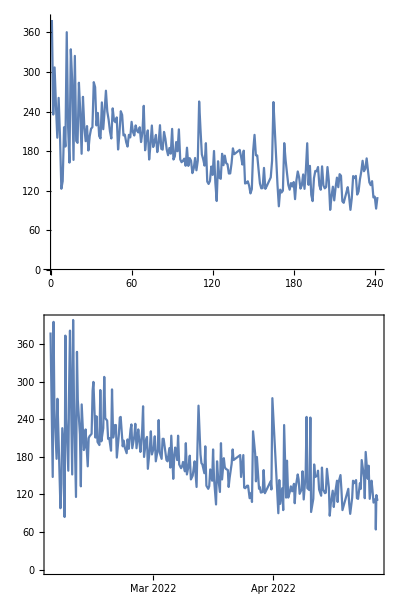

```mathematica
Grid[{{ListLinePlot[InverseFourier[fou],PlotRange->Full]},{dlp}}]
```

少しづつ、ローパスをかけていく。

```mathematica
fouLen=Length[fou]
```

242

```mathematica
np=150
```

150

```mathematica
flt[1]=Table[1,{np}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
flt[2]=Table[0,{fouLen-np}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(flt["total"]=Flatten[{flt[1],flt[2]}])//Length
```

242

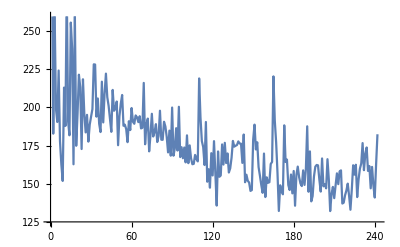

```mathematica
ListLinePlot[InverseFourier[fou*flt["total"]]//Abs]
```

```mathematica
np=100
```

100

```mathematica
flt[1]=Table[1,{np}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
flt[2]=Table[0,{fouLen-np}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(flt["total"]=Flatten[{flt[1],flt[2]}])//Length
```

242

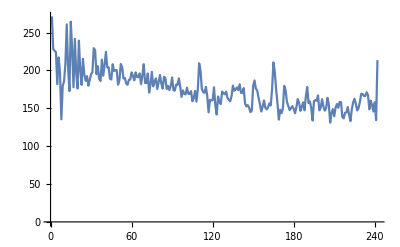

```mathematica
ListLinePlot[InverseFourier[fou*flt["total"]]//Abs]
```

```mathematica
np=50
```

50

```mathematica
flt[1]=Table[1,{np}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
flt[2]=Table[0,{fouLen-np}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(flt["total"]=Flatten[{flt[1],flt[2]}])//Length
```

242

ローパスではあまりうまくいっていないように見える。

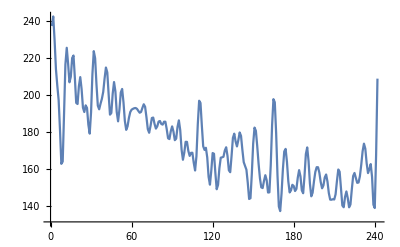

```mathematica
ListLinePlot[InverseFourier[fou*flt["total"]]//Abs]
```

### SemanticImport

```mathematica
semanticData=SemanticImport[dir<>xlsfile]
```

```mathematica
semantic["date","glu"]=Map[{#[[1]],#[[3]]}&,semanticData]
```

```mathematica
semantic["date"]=Map[#[[1]]&,semanticData]
```

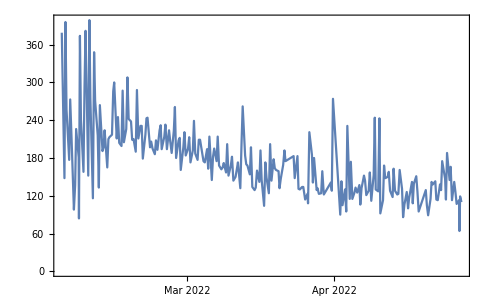

```mathematica
DateListPlot[semantic["date","glu"]]
```

```mathematica
semantic["date"]
```

```mathematica
DateList[semantic["date"][[1]]]
```

{2022,2,2,16,45,0.}

```mathematica
DateList[semantic["date"][[1]]]
```

{2022,2,2,16,45,0.}

```mathematica
AbsoluteTime[semantic["date"][[1]]]
```

3852809100

```mathematica
DateList[semantic["date"][[1]]]
```

{2022,2,2,16,45,0.}

```mathematica
AbsoluteTime[semantic["date"]]
```

AbsoluteTime::arg: 引数Dataset[«241»]は日付または時間入力として解釈することができません．

AbsoluteTime[]